# Exercise 1

First test checking with simplify that I am writing the correct function

```mathematica
x * 1/(e^x)+ x*(1-x)
Simplify[%]
```

e^-x x+(1-x) x

(1+e^-x-x) x

Define the function and plot it to have a reference

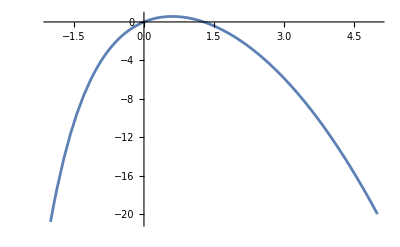

```mathematica
f[x_]:=x*1/(E^x)+x*(1-x)
Plot[f[x],{x,-2,5}]
```

Now evaluating the function

```mathematica
f/@{0,0.1,0.2,0.4,0.8}
```

{0,0.180484,0.323746,0.508128,0.519463}

Attempt for a fancier plot showing the results

{0,0.1,0.2,0.4,0.8}

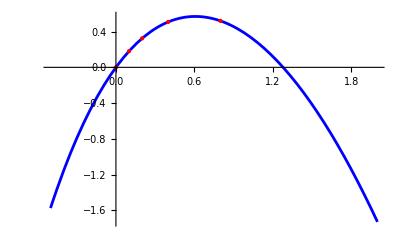

```mathematica
points = {0,0.1,0.2,0.4,0.8}
Show[Plot[f[x],{x,-0.5,2},PlotStyle->Blue,PlotRange->All],ListPlot[Table[{x,f[x]},{x,points}],PlotStyle->{Red,PointSize[Large]},PlotRange->All]]
```